```mathematica
Exp[f'[x]/f[x]]
```

ⅇ^(f'[x]/f[x])

```mathematica
With[{f=#^2&},
ⅇ^(f'[x]/f[x])]
```

ⅇ^(2/x)

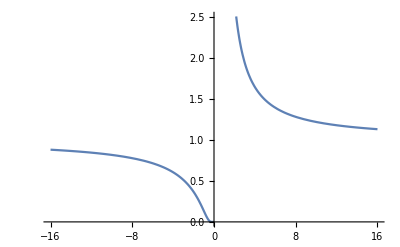

```mathematica
Plot[ⅇ^(2/x),{x,-16,16}]
```

```mathematica
With[{f=2^#&},
ⅇ^(f'[x]/f[x])]
```

2

```mathematica
With[{f=Exp},
ⅇ^(f'[x]/f[x])]
```

ⅇ

```mathematica
With[{f=Log},
ⅇ^(f'[x]/f[x])]
```

ⅇ^(1/(x Log[x]))

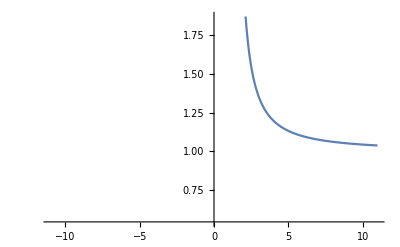

```mathematica
Plot[ⅇ^(1/(x Log[x])),{x,-11.,11.}]
```

```mathematica
With[{f=Identity},
ⅇ^(f'[x]/f[x])]
```

ⅇ^(1/x)

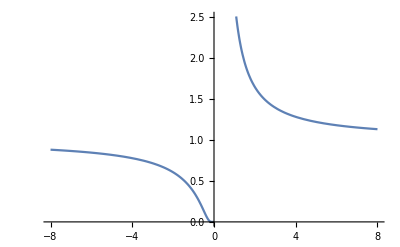

```mathematica
Plot[ⅇ^(1/x),{x,-8,8}]
```

```mathematica
With[{f=#^3&},
ⅇ^(f'[x]/f[x])]
```

ⅇ^(3/x)

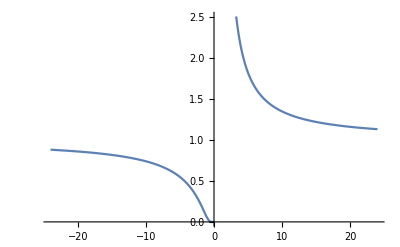

```mathematica
Plot[ⅇ^(3/x),{x,-24,24}]
```

```mathematica
With[{f=2^(3#)&},
ⅇ^(f'[x]/f[x])]
```

8

```mathematica
With[{f=2^(2#)&},
ⅇ^(f'[x]/f[x])]
```

4

```mathematica
With[{f=2^(2^#)&},
ⅇ^(f'[x]/f[x])]
```

ⅇ^(2^x Log[2]^2)

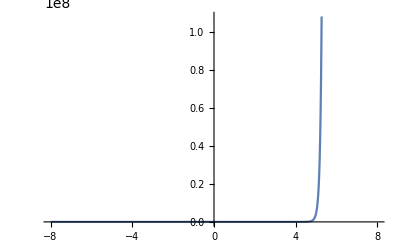

```mathematica
Plot[ⅇ^(2^x Log[2]^2),{x,-8,8}]
```

```mathematica
ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2 π},{v,-π,π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2 π},{v,-π,π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[u],Cos[u],u/10},{u,0,20}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]}},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->{Red,Green}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{1.16^v Cos[v] (1+Cos[u]),-1.16^v Sin[v] (1+Cos[u]),-2 1.16^v (1+Sin[u])},{u,0,2 Pi},{v,-15,6},Mesh->All,PlotRange->All]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u],Sin[u],Sqrt[u]+Sin[5 u]/5},{u,0,4 Pi},Mesh->All]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{v Cos[u],v Sin[u],1/Abs[v Exp[I u]]},{u,0,2 Pi},{v,0,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u Cos[v],u Sin[v],Im[(u Exp[I v]^5)^(1/5)]},{u,0,2},{v,0,2 Pi},Mesh->None,ExclusionsStyle->{None,Red}]
```

-Graphics3D-

```mathematica
Grid[Table[ParametricPlot3D[{Cos[u],Sin[u],Sin[u]},{u,0,2 Pi},PlotPoints->pp,MaxRecursion->mr],{mr,{0,2}},{pp,{5,10}}]]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[Table[{(2+Cos[8 u+i]) Cos[u],(2+Cos[8 u+i]) Sin[u],Sin[8 u+i]},{i,{0,Pi}}]],{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[Table[{(2+Cos[8 u+i]) Cos[u],(2+Cos[8 u+i]) Sin[u],Sin[8 u+i]},{i,{0,Pi}}]],{u,0,2 Pi},PlotStyle->{Blue,Directive[Red,Dashed]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]},{12+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]}},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[v]) Cos[u],(2+Cos[v]) Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]}},{u,0,2 Pi},{v,0,2 Pi},PlotLegends->{"surface1","surface2"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]}},{u,0,2 Pi},{v,0,2 Pi},PlotLegends->{"surface1","surface2"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]}},{u,0,2 Pi},{v,0,2 Pi},PlotLegends->{"surface1","surface2"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[8 u]) Cos[u],(2+Cos[8 u]) Sin[u],Sin[8 u]},{u,0,2 Pi},PlotStyle->Thick,ColorFunction->Function[{x,y,z,u},Hue[u/(2 Pi)]],ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (2 Sin[u]+Cos[u]),Sin[t] (2 Sin[u]+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi},AxesLabel->z]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u Sin[t],u Cos[t],t},{t,0,8},{u,-1,1},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[8 u]) Cos[u],(2+Cos[8 u]) Sin[u],Sin[8 u]},{u,0,2 Pi},Mesh->25,MeshStyle->Directive[PointSize[Medium],Red]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[8 u]) Cos[u],(2+Cos[8 u]) Sin[u],Sin[8 u]},{u,0,2 Pi},Mesh->25,MeshStyle->Directive[PointSize[Medium],Red]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[u],Cos[v],Sin[u] Sin[v]},{u,0,2 Pi},{v,0,2 Pi},Axes->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi},Boxed->False]
```

-Graphics3D-

```mathematica
4 3600
```

14400

```mathematica
(Quantity[4, "Cups"]/Quantity[1, "Seconds"])/Quantity[1, "Devices"]
```

4 cups/(s devices)

```mathematica
20000 14000
```

280000000

```mathematica
a==1/(1+a)
```

a==1/(1+a)

```mathematica
Solve[a==1/(1+a),{a}]
```

{{a→1/2 (-1-√5)},{a→1/2 (-1+√5)}}

```mathematica
N[{{a->1/2 (-1-√5)},{a->1/2 (-1+√5)}}]
```

{{a→-1.61803},{a→0.618034}}

```mathematica
45 6
```

270

```mathematica
40 45
```

1800

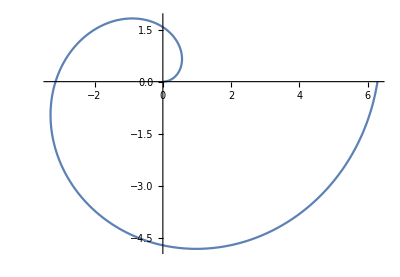

```mathematica
PolarPlot[θ, {θ, 0, 2π}]
```



```mathematica
PolarPlot[1, {θ, 0, 2π}]
```

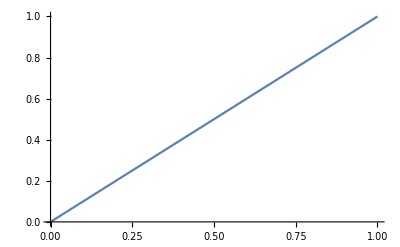

```mathematica
Plot[x, {x, 0, 1}]
```

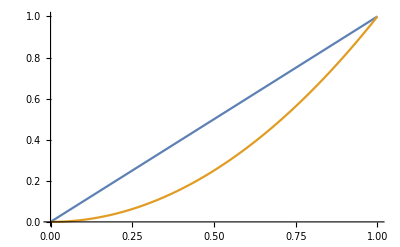

```mathematica
Plot[{x, x^2}, {x, 0, 1}]
```

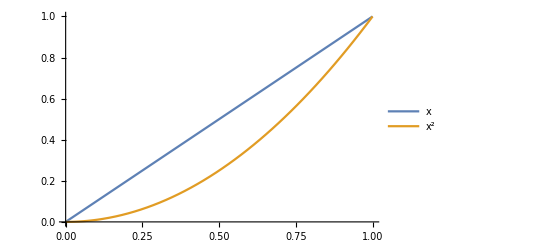

```mathematica
Plot[{x, x^2}, {x, 0, 1}, PlotLegends->"Expressions"]
```

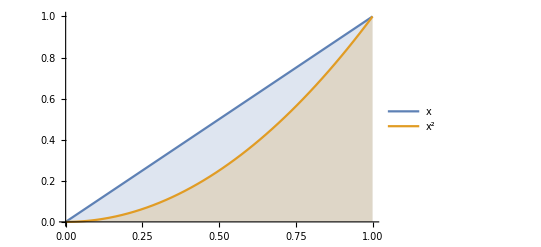

```mathematica
Plot[{x, x^2}, {x, 0, 1}, PlotLegends->"Expressions", Filling->Axis]
```

```mathematica
Plot[{x, x^2}, {x, 0, 1}, PlotLegends->"Expressions", Filling->{1->{{2}}}]
```

Filling::invfillentry: {{2}} is not a valid Filling specification.

-Graphics-

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

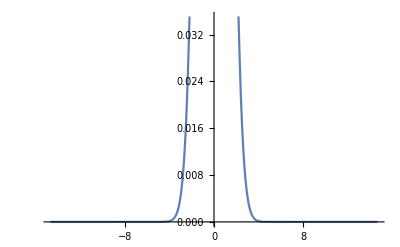

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-14.696938456699069,14.696938456699069}]
```

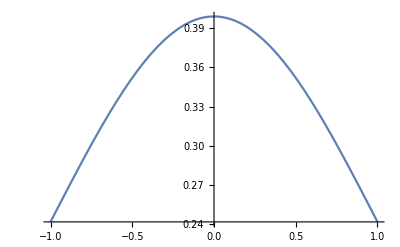

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-1,1}]
```

```mathematica
(ⅇ^(-x^2/2))/(√(2 π))
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
FullForm[(ⅇ^(-x^2/2))/(√(2 π))]
```

Times[Power[E,Times[Rational[-1,2],Power[x,2]]],Power[Times[2,Pi],Rational[-1,2]]]

```mathematica
Head[(ⅇ^(-x^2/2))/(√(2 π))]
```

Times

```mathematica
((ⅇ^(-x^2/2))/(√(2 π)))[[1]]
```

ⅇ^(-x^2/2)

```mathematica
FullForm[((ⅇ^(-x^2/2))/(√(2 π)))[[1]]]
```

Power[E,Times[Rational[-1,2],Power[x,2]]]

```mathematica
CountryData["UnitedStates", "Population"]
```

324459463 people

```mathematica
CountryData["China", "Population"]
```

1409517397 people

```mathematica
CountryData["UnitedStates", "Properties"]
```

{AdultPopulation,AgriculturalProducts,AgriculturalValueAdded,Airports,AlternateNames,AlternateStandardNames,AMRadioStations,AnnualBirths,AnnualDeaths,AnnualHIVAIDSDeaths,ArableLandArea,ArableLandFraction,Area,BirthRateFraction,BorderingCountries,BordersLengths,BoundaryLength,CallingCode,CapitalCity,CapitalLocation,CapitalLocationLink,CellularPhones,CenterCoordinates,CenterLocationLink,ChildPopulation,Classes,ClimateTypes,CoastlineLength,ConstructionValueAdded,Continent,Coordinates,Countries,CountryCode,CropsLandArea,CropsLandFraction,CurrencyCode,CurrencyName,CurrencyShortName,CurrencyUnit,CurrentAccountBalance,DeathRateFraction,Dependencies,DependencyParent,EconomicAid,ElderlyPopulation,ElectricalGridFrequency,ElectricalGridPlugImages,ElectricalGridPlugs,ElectricalGridSocketImages,ElectricalGridSockets,ElectricalGridVoltages,ElectricityConsumption,ElectricityExports,ElectricityImports,ElectricityProduction,EnvironmentalAgreements,EnvironmentalIssues,EthnicGroups,EthnicGroupsFractions,ExchangeRate,ExpenditureFractions,ExportCommodities,ExportPartners,ExportPartnersFractions,ExportValue,ExternalDebt,FemaleAdultPopulation,FemaleChildPopulation,FemaleElderlyPopulation,FemaleInfantMortalityFraction,FemaleLifeExpectancy,FemaleLiteracyFraction,FemaleMedianAge,FemalePopulation,FiscalYearDate,FixedInvestment,Flag,FlagDescription,FMRadioStations,ForeignExchangeReserves,ForeignOwnedShips,ForeignRegisteredShips,FullCoordinates,FullName,FullNativeName,FullPolygon,GDP,GDPAtParity,GDPPerCapita,GDPRealGrowth,GDPSectorFractions,GiniIndex,GovernmentConsumption,GovernmentDebt,GovernmentExpenditures,GovernmentReceipts,GovernmentSurplus,GrossInvestment,Groups,HighestElevation,HighestPoint,HIVAIDSDeathRateFraction,HIVAIDSFraction,HIVAIDSPopulation,HouseholdConsumption,ImportCommodities,ImportPartners,ImportPartnersFractions,ImportValue,IndependenceDate,IndependenceYear,IndustrialProductionGrowth,IndustrialValueAdded,InfantMortalityFraction,InfectiousDiseases,InflationRate,InternationalOrganizations,InternationalOrganizationsObserver,InternetCode,InternetHosts,InternetUsers,InventoryChange,IrrigatedLandArea,IrrigatedLandFraction,ISOName,LaborForce,LandArea,Languages,LanguagesDialects,LanguagesFractions,LargestCities,LifeExpectancy,LiteracyFraction,LowestElevation,LowestPoint,MajorIndustries,MajorPorts,MaleAdultPopulation,MaleChildPopulation,MaleElderlyPopulation,MaleInfantMortalityFraction,MaleLifeExpectancy,MaleLiteracyFraction,MaleMedianAge,MalePopulation,ManufacturingValueAdded,MaritimeClaims,MedianAge,Memberships,MerchantShips,MerchantShipsDeadWeight,MerchantShipsGross,MerchantShipTypes,MigrationRateFraction,MilitaryAgeFemales,MilitaryAgeMales,MilitaryAgePopulation,MilitaryAgeRate,MilitaryExpenditureFraction,MilitaryExpenditures,MilitaryFitFemales,MilitaryFitMales,MilitaryFitPopulation,MiscellaneousValueAdded,Name,NationalIncome,NationalityName,NativeName,NaturalGasConsumption,NaturalGasExports,NaturalGasImports,NaturalGasProduction,NaturalGasReserves,NaturalHazards,NaturalResources,OilConsumption,OilExports,OilImports,OilProduction,OilReserves,PavedAirportLengths,PavedAirports,PavedRoadLength,PhoneLines,Pipelines,Polygon,Population,PopulationGrowth,PovertyFraction,PriceIndex,RadioStations,RailwayGaugeLengths,RailwayGaugeRules,RailwayLength,RegionNames,Regions,Religions,ReligionsFractions,RoadLength,SchematicCoordinates,SchematicPolygon,SectorLaborFractions,Shape,ShortWaveRadioStations,SignedEnvironmentalAgreements,StandardName,SuffrageType,TelevisionStations,TerrainTypes,TimeZones,TotalConsumption,TotalFertilityRate,TradeValueAdded,TransportationValueAdded,UNCode,UnemploymentFraction,UNNumber,UnpavedAirportLengths,UnpavedAirports,UnpavedRoadLength,ValueAdded,WaterArea,WaterwayLength}

```mathematica
CountryData["UnitedStates", "Population"]/CountryData["UnitedStates", "LandArea"]
```

35.4139 people/km^2

```mathematica
CountryData[]
```

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Eswatini,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
CountryData["Europe"]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

```mathematica
CountryData["Africa"]
```

{Algeria,Angola,Benin,Botswana,Burkina Faso,Burundi,Cameroon,Cape Verde,Central African Republic,Chad,Comoros,Democratic Republic of the Congo,Djibouti,Egypt,Equatorial Guinea,Eritrea,Ethiopia,Gabon,Gambia,Ghana,Guinea,Guinea-Bissau,Ivory Coast,Kenya,Lesotho,Liberia,Libya,Madagascar,Malawi,Mali,Mauritania,Mauritius,Mayotte,Morocco,Mozambique,Namibia,Niger,Nigeria,Republic of the Congo,Réunion,Rwanda,Saint Helena, Ascension and Tristan da Cunha,São Tomé and Príncipe,Senegal,Seychelles,Sierra Leone,Somalia,South Africa,South Sudan,Sudan,Eswatini,Tanzania,Togo,Tunisia,Uganda,Western Sahara,Zambia,Zimbabwe}

```mathematica
Map[
CountryData[#, "Population"]&,
CountryData[]]
```

{35530081 people,29013 people,2930187 people,41318142 people,55641 people,76965 people,29784193 people,14909 people,102012 people,44271041 people,2930450 people,105264 people,24450561 people,8735453 people,9827589 people,395361 people,1492584 people,164669751 people,285719 people,9468338 people,11429336 people,374681 people,11175692 people,61349 people,807610 people,11051600 people,21133 people,3507017 people,2291661 people,0 people,209288278 people,2500 people,31196 people,428697 people,7084571 people,19193382 people,10864245 people,16005373 people,24053727 people,36624199 people,546388 people,61559 people,4659080 people,14899994 people,18054726 people,1409517397 people,1513 people,550 people,49065615 people,813912 people,17380 people,4905769 people,4189353 people,11484636 people,160539 people,1179551 people,10618303 people,81339988 people,5733551 people,956985 people,73925 people,10766998 people,1296311 people,16624858 people,97553151 people,6377853 people,1267689 people,5068831 people,1309632 people,104957438 people,2840 people,49290 people,905502 people,5523231 people,64979548 people,282731 people,686371 people,196 people,2025137 people,2100568 people,1763387 people,3912061 people,82114224 people,28833629 people,34571 people,11159773 people,56480 people,107825 people,449568 people,164229 people,16913503 people,65605 people,12717176 people,1861283 people,777859 people,10981229 people,9265067 people,7364883 people,9721559 people,335025 people,1339180127 people,263991379 people,81162788 people,38274618 people,4761657 people,84287 people,8321570 people,59359900 people,24294750 people,2890299 people,127484450 people,95732 people,9702353 people,18204499 people,49699862 people,116398 people,1859203 people,4136528 people,6045117 people,6858160 people,1949670 people,6082357 people,2233339 people,4731906 people,6374616 people,37922 people,2890297 people,583455 people,622567 people,2083159 people,25570895 people,18622104 people,31624264 people,436330 people,18541980 people,430835 people,53127 people,384896 people,4420184 people,1265138 people,253045 people,129163276 people,527530 people,4051212 people,38695 people,3075647 people,628960 people,5177 people,35739580 people,29668834 people,53370609 people,2533794 people,11359 people,29304998 people,17035938 people,276255 people,4705818 people,6217581 people,21477348 people,190886311 people,1618 people,2196 people,55144 people,25490965 people,5305383 people,4636262 people,197015955 people,21729 people,4098587 people,8251162 people,6811297 people,32165485 people,104918090 people,56 people,38170712 people,10329506 people,3663131 people,2639211 people,5260750 people,876562 people,19679306 people,143989754 people,12208407 people,9035 people,4049 people,55345 people,178844 people,36286 people,6320 people,109897 people,196440 people,33400 people,204327 people,32938213 people,15850567 people,8790574 people,94737 people,7557212 people,5708844 people,40120 people,5447662 people,2079976 people,611343 people,14742523 people,56717156 people,30 people,50982212 people,12575714 people,46354321 people,20876917 people,40533330 people,563402 people,2637 people,1367254 people,9910701 people,8476005 people,18269868 people,23626456 people,8921343 people,57310019 people,69037513 people,7797694 people,1300 people,108020 people,1369125 people,11532127 people,80745020 people,5758075 people,35446 people,11192 people,42862958 people,44222947 people,9400145 people,66181585 people,324459463 people,300 people,104901 people,3456750 people,31910641 people,276244 people,792 people,31977065 people,95540800 people,11773 people,2731052 people,552628 people,28250420 people,17094130 people,16529903 people}

```mathematica
Map[
#->CountryData[#, "Population"]&,
CountryData[]]
```

{Afghanistan→35530081 people,Aland Islands→29013 people,Albania→2930187 people,Algeria→41318142 people,American Samoa→55641 people,Andorra→76965 people,Angola→29784193 people,Anguilla→14909 people,Antigua and Barbuda→102012 people,Argentina→44271041 people,Armenia→2930450 people,Aruba→105264 people,Australia→24450561 people,Austria→8735453 people,Azerbaijan→9827589 people,Bahamas→395361 people,Bahrain→1492584 people,Bangladesh→164669751 people,Barbados→285719 people,Belarus→9468338 people,Belgium→11429336 people,Belize→374681 people,Benin→11175692 people,Bermuda→61349 people,Bhutan→807610 people,Bolivia→11051600 people,Caribbean Netherlands→21133 people,Bosnia and Herzegovina→3507017 people,Botswana→2291661 people,Bouvet Island→0 people,Brazil→209288278 people,British Indian Ocean Territory→2500 people,British Virgin Islands→31196 people,Brunei→428697 people,Bulgaria→7084571 people,Burkina Faso→19193382 people,Burundi→10864245 people,Cambodia→16005373 people,Cameroon→24053727 people,Canada→36624199 people,Cape Verde→546388 people,Cayman Islands→61559 people,Central African Republic→4659080 people,Chad→14899994 people,Chile→18054726 people,China→1409517397 people,Christmas Island→1513 people,Cocos Keeling Islands→550 people,Colombia→49065615 people,Comoros→813912 people,Cook Islands→17380 people,Costa Rica→4905769 people,Croatia→4189353 people,Cuba→11484636 people,Curacao→160539 people,Cyprus→1179551 people,Czech Republic→10618303 people,Democratic Republic of the Congo→81339988 people,Denmark→5733551 people,Djibouti→956985 people,Dominica→73925 people,Dominican Republic→10766998 people,East Timor→1296311 people,Ecuador→16624858 people,Egypt→97553151 people,El Salvador→6377853 people,Equatorial Guinea→1267689 people,Eritrea→5068831 people,Estonia→1309632 people,Ethiopia→104957438 people,Falkland Islands→2840 people,Faroe Islands→49290 people,Fiji→905502 people,Finland→5523231 people,France→64979548 people,French Guiana→282731 people,French Polynesia→686371 people,French Southern And Antarctic lands→196 people,Gabon→2025137 people,Gambia→2100568 people,Gaza Strip→1763387 people,Georgia→3912061 people,Germany→82114224 people,Ghana→28833629 people,Gibraltar→34571 people,Greece→11159773 people,Greenland→56480 people,Grenada→107825 people,Guadeloupe→449568 people,Guam→164229 people,Guatemala→16913503 people,Guernsey→65605 people,Guinea→12717176 people,Guinea-Bissau→1861283 people,Guyana→777859 people,Haiti→10981229 people,Honduras→9265067 people,Hong Kong→7364883 people,Hungary→9721559 people,Iceland→335025 people,India→1339180127 people,Indonesia→263991379 people,Iran→81162788 people,Iraq→38274618 people,Ireland→4761657 people,Isle of Man→84287 people,Israel→8321570 people,Italy→59359900 people,Ivory Coast→24294750 people,Jamaica→2890299 people,Japan→127484450 people,Jersey→95732 people,Jordan→9702353 people,Kazakhstan→18204499 people,Kenya→49699862 people,Kiribati→116398 people,Kosovo→1859203 people,Kuwait→4136528 people,Kyrgyzstan→6045117 people,Laos→6858160 people,Latvia→1949670 people,Lebanon→6082357 people,Lesotho→2233339 people,Liberia→4731906 people,Libya→6374616 people,Liechtenstein→37922 people,Lithuania→2890297 people,Luxembourg→583455 people,Macau→622567 people,Macedonia→2083159 people,Madagascar→25570895 people,Malawi→18622104 people,Malaysia→31624264 people,Maldives→436330 people,Mali→18541980 people,Malta→430835 people,Marshall Islands→53127 people,Martinique→384896 people,Mauritania→4420184 people,Mauritius→1265138 people,Mayotte→253045 people,Mexico→129163276 people,Micronesia→527530 people,Moldova→4051212 people,Monaco→38695 people,Mongolia→3075647 people,Montenegro→628960 people,Montserrat→5177 people,Morocco→35739580 people,Mozambique→29668834 people,Myanmar→53370609 people,Namibia→2533794 people,Nauru→11359 people,Nepal→29304998 people,Netherlands→17035938 people,New Caledonia→276255 people,New Zealand→4705818 people,Nicaragua→6217581 people,Niger→21477348 people,Nigeria→190886311 people,Niue→1618 people,Norfolk Island→2196 people,Northern Mariana Islands→55144 people,North Korea→25490965 people,Norway→5305383 people,Oman→4636262 people,Pakistan→197015955 people,Palau→21729 people,Panama→4098587 people,Papua New Guinea→8251162 people,Paraguay→6811297 people,Peru→32165485 people,Philippines→104918090 people,Pitcairn Islands→56 people,Poland→38170712 people,Portugal→10329506 people,Puerto Rico→3663131 people,Qatar→2639211 people,Republic of the Congo→5260750 people,Réunion→876562 people,Romania→19679306 people,Russia→143989754 people,Rwanda→12208407 people,Saint Barthelemy→9035 people,Saint Helena, Ascension and Tristan da Cunha→4049 people,Saint Kitts and Nevis→55345 people,Saint Lucia→178844 people,Saint Martin→36286 people,Saint Pierre and Miquelon→6320 people,Saint Vincent and the Grenadines→109897 people,Samoa→196440 people,San Marino→33400 people,São Tomé and Príncipe→204327 people,Saudi Arabia→32938213 people,Senegal→15850567 people,Serbia→8790574 people,Seychelles→94737 people,Sierra Leone→7557212 people,Singapore→5708844 people,Sint Maarten→40120 people,Slovakia→5447662 people,Slovenia→2079976 people,Solomon Islands→611343 people,Somalia→14742523 people,South Africa→56717156 people,South Georgia and the South Sandwich Islands→30 people,South Korea→50982212 people,South Sudan→12575714 people,Spain→46354321 people,Sri Lanka→20876917 people,Sudan→40533330 people,Suriname→563402 people,Svalbard→2637 people,Eswatini→1367254 people,Sweden→9910701 people,Switzerland→8476005 people,Syria→18269868 people,Taiwan→23626456 people,Tajikistan→8921343 people,Tanzania→57310019 people,Thailand→69037513 people,Togo→7797694 people,Tokelau→1300 people,Tonga→108020 people,Trinidad and Tobago→1369125 people,Tunisia→11532127 people,Turkey→80745020 people,Turkmenistan→5758075 people,Turks and Caicos Islands→35446 people,Tuvalu→11192 people,Uganda→42862958 people,Ukraine→44222947 people,United Arab Emirates→9400145 people,United Kingdom→66181585 people,United States→324459463 people,United States Minor Outlying Islands→300 people,United States Virgin Islands→104901 people,Uruguay→3456750 people,Uzbekistan→31910641 people,Vanuatu→276244 people,Vatican City→792 people,Venezuela→31977065 people,Vietnam→95540800 people,Wallis and Futuna Islands→11773 people,West Bank→2731052 people,Western Sahara→552628 people,Yemen→28250420 people,Zambia→17094130 people,Zimbabwe→16529903 people}

```mathematica
SortBy[
Map[
#->CountryData[#, "Population"]&,
CountryData[]], Last]
```

{Bouvet Island→0 people,South Georgia and the South Sandwich Islands→30 people,Pitcairn Islands→56 people,French Southern And Antarctic lands→196 people,United States Minor Outlying Islands→300 people,Cocos Keeling Islands→550 people,Vatican City→792 people,Tokelau→1300 people,Christmas Island→1513 people,Niue→1618 people,Norfolk Island→2196 people,British Indian Ocean Territory→2500 people,Svalbard→2637 people,Falkland Islands→2840 people,Saint Helena, Ascension and Tristan da Cunha→4049 people,Montserrat→5177 people,Saint Pierre and Miquelon→6320 people,Saint Barthelemy→9035 people,Tuvalu→11192 people,Nauru→11359 people,Wallis and Futuna Islands→11773 people,Anguilla→14909 people,Cook Islands→17380 people,Caribbean Netherlands→21133 people,Palau→21729 people,Aland Islands→29013 people,British Virgin Islands→31196 people,San Marino→33400 people,Gibraltar→34571 people,Turks and Caicos Islands→35446 people,Saint Martin→36286 people,Liechtenstein→37922 people,Monaco→38695 people,Sint Maarten→40120 people,Faroe Islands→49290 people,Marshall Islands→53127 people,Northern Mariana Islands→55144 people,Saint Kitts and Nevis→55345 people,American Samoa→55641 people,Greenland→56480 people,Bermuda→61349 people,Cayman Islands→61559 people,Guernsey→65605 people,Dominica→73925 people,Andorra→76965 people,Isle of Man→84287 people,Seychelles→94737 people,Jersey→95732 people,Antigua and Barbuda→102012 people,United States Virgin Islands→104901 people,Aruba→105264 people,Grenada→107825 people,Tonga→108020 people,Saint Vincent and the Grenadines→109897 people,Kiribati→116398 people,Curacao→160539 people,Guam→164229 people,Saint Lucia→178844 people,Samoa→196440 people,São Tomé and Príncipe→204327 people,Mayotte→253045 people,Vanuatu→276244 people,New Caledonia→276255 people,French Guiana→282731 people,Barbados→285719 people,Iceland→335025 people,Belize→374681 people,Martinique→384896 people,Bahamas→395361 people,Brunei→428697 people,Malta→430835 people,Maldives→436330 people,Guadeloupe→449568 people,Micronesia→527530 people,Cape Verde→546388 people,Western Sahara→552628 people,Suriname→563402 people,Luxembourg→583455 people,Solomon Islands→611343 people,Macau→622567 people,Montenegro→628960 people,French Polynesia→686371 people,Guyana→777859 people,Bhutan→807610 people,Comoros→813912 people,Réunion→876562 people,Fiji→905502 people,Djibouti→956985 people,Cyprus→1179551 people,Mauritius→1265138 people,Equatorial Guinea→1267689 people,East Timor→1296311 people,Estonia→1309632 people,Eswatini→1367254 people,Trinidad and Tobago→1369125 people,Bahrain→1492584 people,Gaza Strip→1763387 people,Kosovo→1859203 people,Guinea-Bissau→1861283 people,Latvia→1949670 people,Gabon→2025137 people,Slovenia→2079976 people,Macedonia→2083159 people,Gambia→2100568 people,Lesotho→2233339 people,Botswana→2291661 people,Namibia→2533794 people,Qatar→2639211 people,West Bank→2731052 people,Lithuania→2890297 people,Jamaica→2890299 people,Albania→2930187 people,Armenia→2930450 people,Mongolia→3075647 people,Uruguay→3456750 people,Bosnia and Herzegovina→3507017 people,Puerto Rico→3663131 people,Georgia→3912061 people,Moldova→4051212 people,Panama→4098587 people,Kuwait→4136528 people,Croatia→4189353 people,Mauritania→4420184 people,Oman→4636262 people,Central African Republic→4659080 people,New Zealand→4705818 people,Liberia→4731906 people,Ireland→4761657 people,Costa Rica→4905769 people,Eritrea→5068831 people,Republic of the Congo→5260750 people,Norway→5305383 people,Slovakia→5447662 people,Finland→5523231 people,Singapore→5708844 people,Denmark→5733551 people,Turkmenistan→5758075 people,Kyrgyzstan→6045117 people,Lebanon→6082357 people,Nicaragua→6217581 people,Libya→6374616 people,El Salvador→6377853 people,Paraguay→6811297 people,Laos→6858160 people,Bulgaria→7084571 people,Hong Kong→7364883 people,Sierra Leone→7557212 people,Togo→7797694 people,Papua New Guinea→8251162 people,Israel→8321570 people,Switzerland→8476005 people,Austria→8735453 people,Serbia→8790574 people,Tajikistan→8921343 people,Honduras→9265067 people,United Arab Emirates→9400145 people,Belarus→9468338 people,Jordan→9702353 people,Hungary→9721559 people,Azerbaijan→9827589 people,Sweden→9910701 people,Portugal→10329506 people,Czech Republic→10618303 people,Dominican Republic→10766998 people,Burundi→10864245 people,Haiti→10981229 people,Bolivia→11051600 people,Greece→11159773 people,Benin→11175692 people,Belgium→11429336 people,Cuba→11484636 people,Tunisia→11532127 people,Rwanda→12208407 people,South Sudan→12575714 people,Guinea→12717176 people,Somalia→14742523 people,Chad→14899994 people,Senegal→15850567 people,Cambodia→16005373 people,Zimbabwe→16529903 people,Ecuador→16624858 people,Guatemala→16913503 people,Netherlands→17035938 people,Zambia→17094130 people,Chile→18054726 people,Kazakhstan→18204499 people,Syria→18269868 people,Mali→18541980 people,Malawi→18622104 people,Burkina Faso→19193382 people,Romania→19679306 people,Sri Lanka→20876917 people,Niger→21477348 people,Taiwan→23626456 people,Cameroon→24053727 people,Ivory Coast→24294750 people,Australia→24450561 people,North Korea→25490965 people,Madagascar→25570895 people,Yemen→28250420 people,Ghana→28833629 people,Nepal→29304998 people,Mozambique→29668834 people,Angola→29784193 people,Malaysia→31624264 people,Uzbekistan→31910641 people,Venezuela→31977065 people,Peru→32165485 people,Saudi Arabia→32938213 people,Afghanistan→35530081 people,Morocco→35739580 people,Canada→36624199 people,Poland→38170712 people,Iraq→38274618 people,Sudan→40533330 people,Algeria→41318142 people,Uganda→42862958 people,Ukraine→44222947 people,Argentina→44271041 people,Spain→46354321 people,Colombia→49065615 people,Kenya→49699862 people,South Korea→50982212 people,Myanmar→53370609 people,South Africa→56717156 people,Tanzania→57310019 people,Italy→59359900 people,France→64979548 people,United Kingdom→66181585 people,Thailand→69037513 people,Turkey→80745020 people,Iran→81162788 people,Democratic Republic of the Congo→81339988 people,Germany→82114224 people,Vietnam→95540800 people,Egypt→97553151 people,Philippines→104918090 people,Ethiopia→104957438 people,Japan→127484450 people,Mexico→129163276 people,Russia→143989754 people,Bangladesh→164669751 people,Nigeria→190886311 people,Pakistan→197015955 people,Brazil→209288278 people,Indonesia→263991379 people,United States→324459463 people,India→1339180127 people,China→1409517397 people}

```mathematica
Reverse@
SortBy[
Map[
#->CountryData[#, "Population"]&,
CountryData[]], Last]
```

{China→1409517397 people,India→1339180127 people,United States→324459463 people,Indonesia→263991379 people,Brazil→209288278 people,Pakistan→197015955 people,Nigeria→190886311 people,Bangladesh→164669751 people,Russia→143989754 people,Mexico→129163276 people,Japan→127484450 people,Ethiopia→104957438 people,Philippines→104918090 people,Egypt→97553151 people,Vietnam→95540800 people,Germany→82114224 people,Democratic Republic of the Congo→81339988 people,Iran→81162788 people,Turkey→80745020 people,Thailand→69037513 people,United Kingdom→66181585 people,France→64979548 people,Italy→59359900 people,Tanzania→57310019 people,South Africa→56717156 people,Myanmar→53370609 people,South Korea→50982212 people,Kenya→49699862 people,Colombia→49065615 people,Spain→46354321 people,Argentina→44271041 people,Ukraine→44222947 people,Uganda→42862958 people,Algeria→41318142 people,Sudan→40533330 people,Iraq→38274618 people,Poland→38170712 people,Canada→36624199 people,Morocco→35739580 people,Afghanistan→35530081 people,Saudi Arabia→32938213 people,Peru→32165485 people,Venezuela→31977065 people,Uzbekistan→31910641 people,Malaysia→31624264 people,Angola→29784193 people,Mozambique→29668834 people,Nepal→29304998 people,Ghana→28833629 people,Yemen→28250420 people,Madagascar→25570895 people,North Korea→25490965 people,Australia→24450561 people,Ivory Coast→24294750 people,Cameroon→24053727 people,Taiwan→23626456 people,Niger→21477348 people,Sri Lanka→20876917 people,Romania→19679306 people,Burkina Faso→19193382 people,Malawi→18622104 people,Mali→18541980 people,Syria→18269868 people,Kazakhstan→18204499 people,Chile→18054726 people,Zambia→17094130 people,Netherlands→17035938 people,Guatemala→16913503 people,Ecuador→16624858 people,Zimbabwe→16529903 people,Cambodia→16005373 people,Senegal→15850567 people,Chad→14899994 people,Somalia→14742523 people,Guinea→12717176 people,South Sudan→12575714 people,Rwanda→12208407 people,Tunisia→11532127 people,Cuba→11484636 people,Belgium→11429336 people,Benin→11175692 people,Greece→11159773 people,Bolivia→11051600 people,Haiti→10981229 people,Burundi→10864245 people,Dominican Republic→10766998 people,Czech Republic→10618303 people,Portugal→10329506 people,Sweden→9910701 people,Azerbaijan→9827589 people,Hungary→9721559 people,Jordan→9702353 people,Belarus→9468338 people,United Arab Emirates→9400145 people,Honduras→9265067 people,Tajikistan→8921343 people,Serbia→8790574 people,Austria→8735453 people,Switzerland→8476005 people,Israel→8321570 people,Papua New Guinea→8251162 people,Togo→7797694 people,Sierra Leone→7557212 people,Hong Kong→7364883 people,Bulgaria→7084571 people,Laos→6858160 people,Paraguay→6811297 people,El Salvador→6377853 people,Libya→6374616 people,Nicaragua→6217581 people,Lebanon→6082357 people,Kyrgyzstan→6045117 people,Turkmenistan→5758075 people,Denmark→5733551 people,Singapore→5708844 people,Finland→5523231 people,Slovakia→5447662 people,Norway→5305383 people,Republic of the Congo→5260750 people,Eritrea→5068831 people,Costa Rica→4905769 people,Ireland→4761657 people,Liberia→4731906 people,New Zealand→4705818 people,Central African Republic→4659080 people,Oman→4636262 people,Mauritania→4420184 people,Croatia→4189353 people,Kuwait→4136528 people,Panama→4098587 people,Moldova→4051212 people,Georgia→3912061 people,Puerto Rico→3663131 people,Bosnia and Herzegovina→3507017 people,Uruguay→3456750 people,Mongolia→3075647 people,Armenia→2930450 people,Albania→2930187 people,Jamaica→2890299 people,Lithuania→2890297 people,West Bank→2731052 people,Qatar→2639211 people,Namibia→2533794 people,Botswana→2291661 people,Lesotho→2233339 people,Gambia→2100568 people,Macedonia→2083159 people,Slovenia→2079976 people,Gabon→2025137 people,Latvia→1949670 people,Guinea-Bissau→1861283 people,Kosovo→1859203 people,Gaza Strip→1763387 people,Bahrain→1492584 people,Trinidad and Tobago→1369125 people,Eswatini→1367254 people,Estonia→1309632 people,East Timor→1296311 people,Equatorial Guinea→1267689 people,Mauritius→1265138 people,Cyprus→1179551 people,Djibouti→956985 people,Fiji→905502 people,Réunion→876562 people,Comoros→813912 people,Bhutan→807610 people,Guyana→777859 people,French Polynesia→686371 people,Montenegro→628960 people,Macau→622567 people,Solomon Islands→611343 people,Luxembourg→583455 people,Suriname→563402 people,Western Sahara→552628 people,Cape Verde→546388 people,Micronesia→527530 people,Guadeloupe→449568 people,Maldives→436330 people,Malta→430835 people,Brunei→428697 people,Bahamas→395361 people,Martinique→384896 people,Belize→374681 people,Iceland→335025 people,Barbados→285719 people,French Guiana→282731 people,New Caledonia→276255 people,Vanuatu→276244 people,Mayotte→253045 people,São Tomé and Príncipe→204327 people,Samoa→196440 people,Saint Lucia→178844 people,Guam→164229 people,Curacao→160539 people,Kiribati→116398 people,Saint Vincent and the Grenadines→109897 people,Tonga→108020 people,Grenada→107825 people,Aruba→105264 people,United States Virgin Islands→104901 people,Antigua and Barbuda→102012 people,Jersey→95732 people,Seychelles→94737 people,Isle of Man→84287 people,Andorra→76965 people,Dominica→73925 people,Guernsey→65605 people,Cayman Islands→61559 people,Bermuda→61349 people,Greenland→56480 people,American Samoa→55641 people,Saint Kitts and Nevis→55345 people,Northern Mariana Islands→55144 people,Marshall Islands→53127 people,Faroe Islands→49290 people,Sint Maarten→40120 people,Monaco→38695 people,Liechtenstein→37922 people,Saint Martin→36286 people,Turks and Caicos Islands→35446 people,Gibraltar→34571 people,San Marino→33400 people,British Virgin Islands→31196 people,Aland Islands→29013 people,Palau→21729 people,Caribbean Netherlands→21133 people,Cook Islands→17380 people,Anguilla→14909 people,Wallis and Futuna Islands→11773 people,Nauru→11359 people,Tuvalu→11192 people,Saint Barthelemy→9035 people,Saint Pierre and Miquelon→6320 people,Montserrat→5177 people,Saint Helena, Ascension and Tristan da Cunha→4049 people,Falkland Islands→2840 people,Svalbard→2637 people,British Indian Ocean Territory→2500 people,Norfolk Island→2196 people,Niue→1618 people,Christmas Island→1513 people,Tokelau→1300 people,Vatican City→792 people,Cocos Keeling Islands→550 people,United States Minor Outlying Islands→300 people,French Southern And Antarctic lands→196 people,Pitcairn Islands→56 people,South Georgia and the South Sandwich Islands→30 people,Bouvet Island→0 people}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Map[
#->#^2&,
Range[10]]
```

{1→1,2→4,3→9,4→16,5→25,6→36,7→49,8→64,9→81,10→100}

```mathematica
FullForm[{1->1,2->4,3->9,4->16,5->25,6->36,7->49,8->64,9->81,10->100}]
```

List[Rule[1,1],Rule[2,4],Rule[3,9],Rule[4,16],Rule[5,25],Rule[6,36],Rule[7,49],Rule[8,64],Rule[9,81],Rule[10,100]]

```mathematica
Hold[
Map[
#->#^2&,
Range[10]]]
```

Hold[(#1→#1^2&)/@Range[10]]

```mathematica
ReleaseHold[Hold[(#1->#1^2&)/@Range[10]]]
```

{1→1,2→4,3→9,4→16,5→25,6→36,7→49,8→64,9→81,10→100}

```mathematica
Reverse@
SortBy[
Map[
#->CountryData[#, "Population"]/CountryData[#, "LandArea"]&,
CountryData[]], Last]
```

{Macau→22076.8 people/km^2,Monaco→19347.5 people/km^2,Singapore→8309.82 people/km^2,Hong Kong→6987.56 people/km^2,Gibraltar→5318.62 people/km^2,Gaza Strip→4898.3 people/km^2,Bahrain→1963.93 people/km^2,Vatican City→1800. people/km^2,Maldives→1464.19 people/km^2,Malta→1363.4 people/km^2,Bangladesh→1265.06 people/km^2,Sint Maarten→1180. people/km^2,Bermuda→1136.09 people/km^2,Guernsey→841.09 people/km^2,Jersey→825.276 people/km^2,Micronesia→751.467 people/km^2,Taiwan→732.376 people/km^2,Saint Martin→682.068 people/km^2,Mayotte→676.591 people/km^2,Barbados→664.463 people/km^2,Mauritius→623.221 people/km^2,Lebanon→591.554 people/km^2,Aruba→584.8 people/km^2,San Marino→547.541 people/km^2,Nauru→540.905 people/km^2,South Korea→519.22 people/km^2,Netherlands→502.639 people/km^2,Rwanda→494.909 people/km^2,West Bank→484.229 people/km^2,India→450.418 people/km^2,Tuvalu→430.462 people/km^2,Burundi→423.063 people/km^2,Puerto Rico→412.98 people/km^2,Israel→409.325 people/km^2,Haiti→398.448 people/km^2,Belgium→377.48 people/km^2,Comoros→364.166 people/km^2,Martinique→363.109 people/km^2,Curacao→361.574 people/km^2,Saint Barthelemy→361.4 people/km^2,Philippines→351.873 people/km^2,Réunion→349.646 people/km^2,Japan→340.191 people/km^2,Sri Lanka→323.022 people/km^2,Grenada→313.445 people/km^2,El Salvador→307.797 people/km^2,United States Virgin Islands→303.182 people/km^2,Guam→301.892 people/km^2,Saint Lucia→295.122 people/km^2,Vietnam→293.646 people/km^2,Marshall Islands→293.519 people/km^2,Saint Vincent and the Grenadines→282.512 people/km^2,American Samoa→279.603 people/km^2,United Kingdom→273.557 people/km^2,Trinidad and Tobago→266.99 people/km^2,Jamaica→266.854 people/km^2,Guadeloupe→263.522 people/km^2,Pakistan→255.574 people/km^2,Liechtenstein→237.013 people/km^2,Germany→235.506 people/km^2,Cayman Islands→233.178 people/km^2,Kuwait→232.154 people/km^2,Antigua and Barbuda→230.484 people/km^2,Qatar→227.793 people/km^2,Luxembourg→225.621 people/km^2,Dominican Republic→222.827 people/km^2,Uganda→214.626 people/km^2,Saint Kitts and Nevis→212.05 people/km^2,São Tomé and Príncipe→211.957 people/km^2,Switzerland→211.916 people/km^2,North Korea→211.705 people/km^2,Gambia→210.057 people/km^2,Nigeria→209.588 people/km^2,Seychelles→208.213 people/km^2,British Virgin Islands→206.596 people/km^2,Nepal→204.428 people/km^2,Italy→201.808 people/km^2,Malawi→197.939 people/km^2,French Polynesia→179.35 people/km^2,Kosovo→170.773 people/km^2,Andorra→164.455 people/km^2,Anguilla→163.835 people/km^2,Guatemala→157.836 people/km^2,China→151.132 people/km^2,Tonga→150.656 people/km^2,Isle of Man→147.355 people/km^2,Indonesia→145.725 people/km^2,Kiribati→143.524 people/km^2,Togo→143.379 people/km^2,Czech Republic→137.459 people/km^2,Cape Verde→135.479 people/km^2,Thailand→135.132 people/km^2,Denmark→135.117 people/km^2,Cyprus→127.643 people/km^2,Ghana→126.723 people/km^2,Poland→125.456 people/km^2,Moldova→123.171 people/km^2,Azerbaijan→118.936 people/km^2,Northern Mariana Islands→118.845 people/km^2,France→118.151 people/km^2,Serbia→113.465 people/km^2,Slovakia→113.245 people/km^2,Portugal→112.928 people/km^2,United Arab Emirates→112.442 people/km^2,Jordan→109.258 people/km^2,Hungary→108.49 people/km^2,Tokelau→108.333 people/km^2,Albania→106.949 people/km^2,Austria→105.955 people/km^2,Sierra Leone→105.518 people/km^2,Turkey→104.914 people/km^2,Cuba→104.577 people/km^2,Armenia→103.906 people/km^2,Slovenia→103.219 people/km^2,Benin→101.026 people/km^2,Syria→99.4928 people/km^2,Dominica→98.4354 people/km^2,Egypt→97.999 people/km^2,Malaysia→96.2227 people/km^2,Costa Rica→96.0785 people/km^2,Ethiopia→93.7385 people/km^2,Spain→92.8982 people/km^2,Cambodia→90.6743 people/km^2,Iraq→88.5654 people/km^2,Kenya→87.3245 people/km^2,East Timor→87.1528 people/km^2,Romania→85.6028 people/km^2,Greece→85.3194 people/km^2,Wallis and Futuna Islands→82.9085 people/km^2,Honduras→82.8051 people/km^2,Senegal→82.3278 people/km^2,Macedonia→81.9077 people/km^2,Myanmar→81.6679 people/km^2,Brunei→81.4239 people/km^2,Morocco→80.0797 people/km^2,Eswatini→79.473 people/km^2,United States Minor Outlying Islands→76.9231 people/km^2,Ivory Coast→76.3979 people/km^2,Ukraine→76.3346 people/km^2,Uzbekistan→75.0133 people/km^2,Croatia→74.8446 people/km^2,Tunisia→74.2284 people/km^2,Cook Islands→73.6441 people/km^2,Lesotho→73.574 people/km^2,Burkina Faso→70.1 people/km^2,Samoa→69.6349 people/km^2,Ireland→69.1267 people/km^2,Bosnia and Herzegovina→68.5138 people/km^2,Mexico→66.4439 people/km^2,Guinea-Bissau→66.1907 people/km^2,Bulgaria→65.3022 people/km^2,Tanzania→64.6986 people/km^2,Caribbean Netherlands→64.4299 people/km^2,Tajikistan→63.0439 people/km^2,Norfolk Island→61. people/km^2,Ecuador→60.052 people/km^2,Georgia→56.1271 people/km^2,Panama→55.133 people/km^2,Afghanistan→54.4748 people/km^2,Yemen→53.5078 people/km^2,Nicaragua→51.8175 people/km^2,Guinea→51.7554 people/km^2,Cameroon→50.8847 people/km^2,Montserrat→50.7549 people/km^2,Eritrea→50.1864 people/km^2,Iran→49.6105 people/km^2,Fiji→49.5514 people/km^2,Liberia→49.1269 people/km^2,Palau→47.3399 people/km^2,Colombia→47.2375 people/km^2,Montenegro→46.7559 people/km^2,South Africa→46.7012 people/km^2,Belarus→46.665 people/km^2,Lithuania→46.1119 people/km^2,Equatorial Guinea→45.1923 people/km^2,Madagascar→43.971 people/km^2,Zimbabwe→42.7298 people/km^2,British Indian Ocean Territory→41.6667 people/km^2,Djibouti→41.2849 people/km^2,Bahamas→39.4966 people/km^2,Cocos Keeling Islands→39.2857 people/km^2,Mozambique→37.7284 people/km^2,Turks and Caicos Islands→37.3903 people/km^2,Venezuela→36.2531 people/km^2,Democratic Republic of the Congo→35.8793 people/km^2,United States→35.4139 people/km^2,Faroe Islands→35.3841 people/km^2,Kyrgyzstan→31.5177 people/km^2,Latvia→31.3205 people/km^2,Estonia→30.8963 people/km^2,Laos→29.7147 people/km^2,Saint Pierre and Miquelon→26.1157 people/km^2,Peru→25.1294 people/km^2,Brazil→24.7403 people/km^2,Chile→24.2732 people/km^2,Sweden→24.1527 people/km^2,Angola→23.8904 people/km^2,Somalia→23.5002 people/km^2,Zambia→22.9946 people/km^2,Sudan→22.6651 people/km^2,Vanuatu→22.6634 people/km^2,Solomon Islands→21.8446 people/km^2,South Sudan→21.4004 people/km^2,Bhutan→21.0348 people/km^2,Uruguay→19.7512 people/km^2,Aland Islands→18.36 people/km^2,Papua New Guinea→18.2201 people/km^2,Finland→18.1796 people/km^2,New Zealand→17.5576 people/km^2,Norway→17.4357 people/km^2,Algeria→17.3479 people/km^2,Paraguay→17.1439 people/km^2,Niger→16.9554 people/km^2,Saudi Arabia→16.8002 people/km^2,Belize→16.4291 people/km^2,Argentina→16.1769 people/km^2,Republic of the Congo→15.4048 people/km^2,Mali→15.196 people/km^2,New Caledonia→15.1166 people/km^2,Oman→14.9798 people/km^2,Turkmenistan→12.253 people/km^2,Chad→11.8329 people/km^2,Christmas Island→11.2074 people/km^2,Bolivia→10.2018 people/km^2,Saint Helena, Ascension and Tristan da Cunha→9.80387 people/km^2,Russia→71994877/8188871 people/km^2,Gabon→7.85951 people/km^2,Central African Republic→7.47865 people/km^2,Kazakhstan→6.74316 people/km^2,Niue→6.22308 people/km^2,Mauritania→4.28853 people/km^2,Botswana→4.04366 people/km^2,Canada→4.02751 people/km^2,Guyana→3.95155 people/km^2,Libya→3.62289 people/km^2,Suriname→3.61155 people/km^2,Iceland→3.3419 people/km^2,Australia→3.18271 people/km^2,French Guiana→3.17141 people/km^2,Namibia→3.07764 people/km^2,Western Sahara→2.07755 people/km^2,Mongolia→1.97975 people/km^2,Pitcairn Islands→1.19149 people/km^2,Falkland Islands→0.233303 people/km^2,Svalbard→0.0425014 people/km^2,Greenland→0.0260747 people/km^2,South Georgia and the South Sandwich Islands→0.0076864 people/km^2,French Southern And Antarctic lands→0.000445676 people/km^2,Bouvet Island→0. people/km^2}

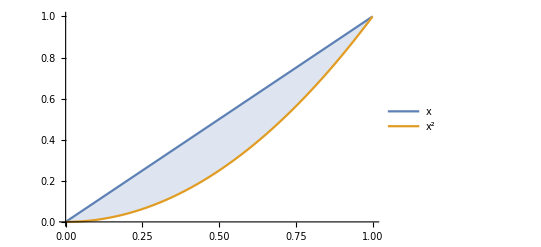

```mathematica
Plot[{x, x^2}, {x, 0, 1}, PlotLegends->"Expressions", Filling->{1->{2}}]
```

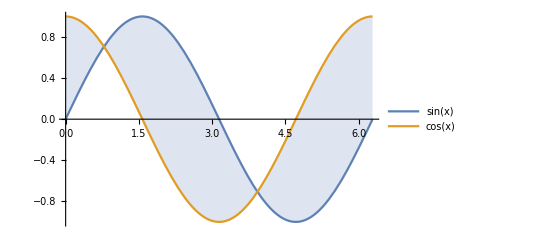

```mathematica
Plot[{Sin@x, Cos@x}, {x, 0, 2π}, PlotLegends->"Expressions", Filling->{1->{2}}]
```

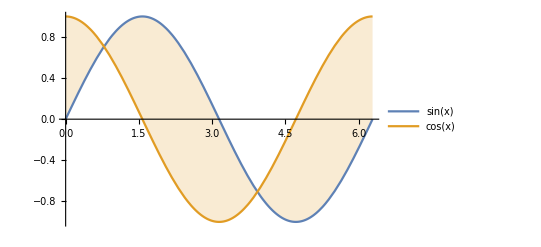

```mathematica
Plot[{Sin@x, Cos@x}, {x, 0, 2π}, PlotLegends->"Expressions", Filling->{2->{1}}]
```

```mathematica
ParametricPlot3D[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},{ϕ,-π,π},{θ,0,π},RegionFunction->(Sin[5 (#4+#5)]>0&),Mesh->None,BoundaryStyle->Black]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},{ϕ,-π,π},{θ,0,π},RegionFunction->(Sin[5 (#4+#5)]>0&),Mesh->None,BoundaryStyle->Black]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.s],{t,0,200},PlotPoints->100,ColorFunction->(Hue[#4]&)]
```

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
s=NDSolve[{Derivative[1][x][t]==-3 (x[t]-y[t]),Derivative[1][y][t]==-x[t] z[t]+26.5 x[t]-y[t],Derivative[1][z][t]==x[t] y[t]-z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,200},MaxSteps->∞]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.s],{t,0,200},PlotPoints->100,ColorFunction->(Hue[#4]&)]
```

-Graphics3D-

```mathematica
intrinsicCurve3D[{κ_,τ_},{s_,smin_,smax_},{s0_,x0_,t0_,n0_}]:=Module[{x,t,n,b},x/.First@NDSolve[{x'[s]==t[s],x[s0]==x0,t'[s]==κ n[s],t[s0]==t0,n'[s]==τ b[s]-κ t[s],n[s0]==n0,b'[s]==-τ n[s],b[s0]==t0×n0},{x,t,n,b},{s,smin,smax}]];
```

```mathematica
intrinsicCurve3D[{κ_,τ_},{s_,smin_,smax_}]:=intrinsicCurve3D[{κ,τ},{s,smin,smax},{0,{0,0,0},{1,0,0},{0,1,0}}];
```

```mathematica
ParametricPlot3D[Evaluate@intrinsicCurve3D[{Abs[s],0.3},{s,-10,10}][s],{s,-10,10}]
```

NDSolve::dsvar: {x→InterpolatingFunction[{{0.,200.}},«3»,{Automatic}],y→«1»,z→InterpolatingFunction[{{0.,200.}},«3»,{«9»}]} cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate@intrinsicCurve3D[{Abs[s],0.3},{s,-10,10}][s],{s,-10,10}]
```

NDSolve::dsvar: {x→InterpolatingFunction[{{0.,200.}},«3»,{Automatic}],y→«1»,z→InterpolatingFunction[{{0.,200.}},«3»,{«9»}]} cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate@intrinsicCurve3D[{Abs[s],0.3},{s,-10,10}][s],{s,-10,10}]
```

NDSolve::dsvar: {x→InterpolatingFunction[{{0.,200.}},«3»,{Automatic}],y→«1»,z→InterpolatingFunction[{{0.,200.}},«3»,{«9»}]} cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2==z^2,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t,0, 2π}]
```

-Graphics-

```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t,0, 2π}]
```

-Graphics-

```mathematica
40 45
```

1800

```mathematica
12 7 45
```

3780

```mathematica
12 7 45 4
```

15120

```mathematica
SphericalPlot3D[1+2 Cos[2 θ],{θ,0,Pi},{ϕ,0,2 Pi}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{1,2,3},{θ,0,Pi},{ϕ,0,3 Pi/2}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5 ϕ]/5,{θ,0,Pi},{ϕ,0,2 Pi},PlotStyle->Directive[Orange,Opacity[0.7],Specularity[White,10]],Mesh->None,PlotPoints->30]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{ϕ,-ϕ},{θ,-Pi/2,Pi/2},{ϕ,0,3 Pi/2},PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
{t^2-1,t(t^2-1)}
```

{-1+t^2,t (-1+t^2)}

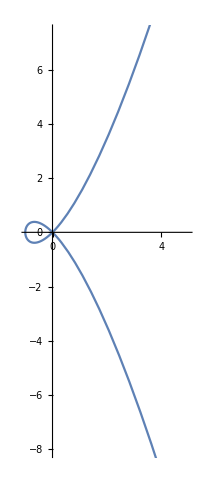

```mathematica
ParametricPlot[{-1+t^2,t (-1+t^2)},{t,-2.449489742783178,2.449489742783178}]
```

```mathematica
D[{-1+t^2,t (-1+t^2)},t]
```

{2 t,-1+3 t^2}

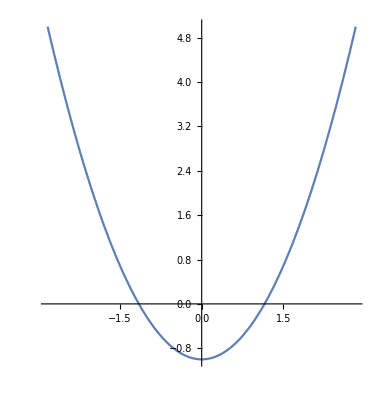

```mathematica
ParametricPlot[{2 t,-1+3 t^2},{t,-1.4142135623730954,1.4142135623730954}]
```

```mathematica
Plot3D[0, {x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
FullForm[Plot3D[0, {x, -2, 2}, {y, -2, 2}]]
```

Graphics3D[GraphicsComplex[List[List[-2.,-2.,0.],1306,List[1.75,-1.75,0.]],List[1,1],Rule[VertexNormals,List[List[0.,0.,1.],1306,List[0.,0.,1.]]]],1]
 |  |  |  |

```mathematica
Show[{
ParametricPlot3D[{-1+t^2,t (-1+t^2),0},{t,-2,2}],
Plot3D[0, {x, -2, 2}, {y, -2, 2}]}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[{-1+t^2,t (-1+t^2),1},{t,-2,2}],
Plot3D[1, {x, -2, 2}, {y, -2, 2}]}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[{
{-1+t^2,t (-1+t^2),0},
{-1+t^2,t (-1+t^2),1}},{t,-2,2}],
Plot3D[{0,1}, {x, -2, 2}, {y, -2, 2}]}]
```

-Graphics3D-

```mathematica
∫_a^b f[x]ⅆx
```

∫_a^b f[x]ⅆx

```mathematica
FullForm[∫_a^b f[x]ⅆx]
```

Integrate[f[x],List[x,a,b]]

```mathematica
∫_a^b f[x]ⅆx{a,b}
```

{-f[a],f[b]}

```mathematica
Plot3D[0, {x, -1, 1}, {y ,-1, 1}]
```

-Graphics3D-

```mathematica
a^2+b^2+c^2==d^2
```

a^2+b^2+c^2==d^2

```mathematica
Solve[a^2+b^2+c^2==d^2,d]
```

{{d→-√(a^2+b^2+c^2)},{d→√(a^2+b^2+c^2)}}

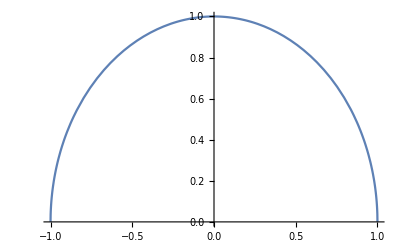

```mathematica
Plot[√(1-x^2),{x,-1,1}]
```

```mathematica
Plot3D[√(1-x^2-y^2),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Manipulate[
Plot3D[(1-a)0+a (√(1-x^2-y^2)), Element[{x,y},Disk[{0,0},1]], PlotRange->{0, 1}],
{a, 0, 1, .1}]
```

```mathematica
Sin[x]/x
```

Sin[x]/x

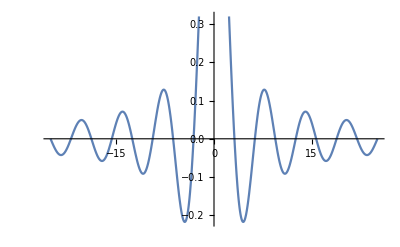

```mathematica
Plot[Sin[x]/x,{x,-25.132741228718345,25.132741228718345}]
```

```mathematica
1/Sin[x]
```

Csc[x]

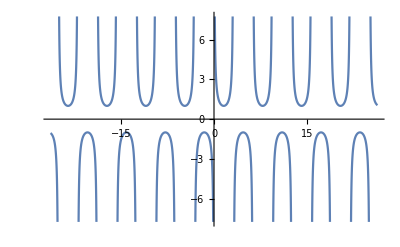

```mathematica
Plot[Csc[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
x/Sin[x]
```

x Csc[x]

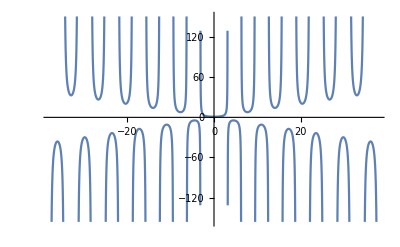

```mathematica
Plot[x Csc[x],{x,-37.69911184307752,37.69911184307752}]
```

```mathematica
Sin[1/x]
```

Sin[1/x]

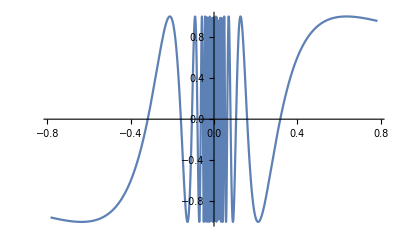

```mathematica
Plot[Sin[1/x],{x,-π/4,π/4}]
```

```mathematica
Plot[Sin[1/x],{x,-π/4,π/4}]
```

```mathematica
Show[{
ParametricPlot3D[
{t,Sin[1/t],t},{t,-1,1}],
Plot3D[{0,x,y}, {x, -2, 2}, {y, -2, 2}]}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{t,Sin[1/t],t^2},{t,-1,1}],
Plot3D[{0,x,y,x^2}, {x, -2, 2}, {y, -2, 2}]}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{t,Sin[1/t],√(1-t^2)},{t,-1,1}],
Plot3D[{0,√(1-x^2)}, {x, -2, 2}, {y, -2, 2}]}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{t,Sin[1/t],√(1-t^2)},{t,-1,1}],
Plot3D[{0,√(1-x^2)},{x,-1,1}, {y,-1,1}]}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{t,Sin[10t],√(1-t^2)},{t,-1,1}],
Plot3D[{0,√(1-x^2)},{x,-1,1}, {y,-1,1}]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{t,Sin[10t],√(1-t^2)},{t,-1,1}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{t,Sin[10t],√(1-t^2-Sin[10t]^2)},{t,-1,1}],
Plot3D[{0,√(1-x^2-y^2)},{x,-1,1}, {y,-1,1}]}]
```

-Graphics3D-

```mathematica
Show[%137,Boxed->False]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{t,Sin[10t],√(1-t^2-Sin[10t]^2)},{t,-1,1}],
Plot3D[{0,√(1-x^2-y^2)},{x,-1,1}, {y,-1,1}]}]
```

```mathematica
ParametricPlot3D[
{t,Sin[10t],√(1-t^2)},{t,-1,1},
ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{t,Sin[10t],√(1-t^2-Sin[10t]^2)},{t,-1,1}, ColorFunction->"Rainbow"],
Plot3D[{√(1-x^2-y^2)},{x,-1,1}, {y,-1,1}]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u Sin[t],u Cos[t],t},{t,0,8},{u,-1,1},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t},{t,0,4π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],t},{t,0,4π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{u Sin[t],u Cos[t],t},
{Cos[t], Sin[t],t}},
{t,0,8},{u,-1,1},
BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[{-1+t^2,t (-1+t^2),0},{t,-2,2}],
Plot3D[0, {x, -2, 2}, {y, -2, 2}]}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[{-1+t^2,t (-1+t^2),√(1-(t^2-1)^2-(t(t^2-1))^2)},{t,-4,4}],
Plot3D[√(1-x^2-y^2), {x, -4,4}, {y, -4, 4}]}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[{-1+t^2,t (-1+t^2),√(1-(t^2-1)^2-(t(t^2-1))^2)},{t,-4,4}, ColorFunction->"Rainbow"],
Plot3D[√(1-x^2-y^2), {x, -4,4}, {y, -4, 4}]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{-1+t^2,t (-1+t^2),
√(1-(t^2-1)^2-(t(t^2-1))^2)},
{t,-4,4},
 ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
{-1+t^2,t (-1+t^2),
√(1-(t^2-1)^2-(t(t^2-1))^2)}
```

{-1+t^2,t (-1+t^2),√(1-(-1+t^2)^2-t^2 (-1+t^2)^2)}

```mathematica
D[{-1+t^2,t (-1+t^2),√(1-(-1+t^2)^2-t^2 (-1+t^2)^2)},t]
```

{2 t,-1+3 t^2,(-4 t (-1+t^2)-4 t^3 (-1+t^2)-2 t (-1+t^2)^2)/(2 √(1-(-1+t^2)^2-t^2 (-1+t^2)^2))}

```mathematica
∫_-4^4 √((2t)^2+(3 t^2-1)^2)ⅆt
```

∫_-4^4 √(4 t^2+(-1+3 t^2)^2)ⅆt

```mathematica
NIntegrate[√(4 t^2+(-1+3 t^2)^2),{t,-4,4}]
```

126.948

```mathematica
FullSimplify[
(2t)^2+(3 t^2-1)^2, Element[t,Reals]]
```

1-2 t^2+9 t^4

```mathematica
Solve[1-2 t^2+9 t^4==0,t]
```

{{t→-√(1/9-(2 ⅈ √2)/9)},{t→√(1/9-(2 ⅈ √2)/9)},{t→-√(1/9+(2 ⅈ √2)/9)},{t→√(1/9+(2 ⅈ √2)/9)}}

```mathematica
∫_-4^4 √(1-2 t^2+9 t^4)ⅆt
```

∫_-4^4 √(1-2 t^2+9 t^4)ⅆt

```mathematica
NIntegrate[√(1-2 t^2+9 t^4),{t,-4,4}]
```

126.948

```mathematica
10000 100
```

1000000

```mathematica
20000 2 4
```

160000

```mathematica
160000/10000
```

16

```mathematica
Show[{
ParametricPlot3D[{-1+t^2,t (-1+t^2),√(1-(t^2-1)^2-(t(t^2-1))^2)},{t,-4,4}, ColorFunction->"Rainbow"],
Plot3D[√(1-x^2-y^2), {x, -4,4}, {y, -4, 4}, ColorFunction->"Rainbow"]}]
```

-Graphics3D-

```mathematica
1==∫_0^a f[x]ⅆx
```

1==∫_0^a f[x]ⅆx

```mathematica
1==∫_0^a √(1+f'[x]^2)ⅆx
```

1==∫_0^a √(1+f'[x]^2)ⅆx

```mathematica
Reduce[1==∫_0^a √(1+f'[x]^2)ⅆx]
```

∫_0^a √(1+f'[x]^2)ⅆx==1

```mathematica
With[{f=Identity},
1==∫_0^a √(1+f'[x]^2)ⅆx]
```

1==√2 a

```mathematica
Reduce[1==√2 a]
```

a==1/(√2)

```mathematica
With[{f=Identity},
Reduce[1==∫_0^a √(1+f'[x]^2)ⅆx,a,Reals]]
```

a==1/(√2)

```mathematica
With[{f=Sin},
Reduce[1==∫_0^a √(1+f'[x]^2)ⅆx,a,Reals]]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[ConditionalExpression[1==√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π]),a∈ℝ],a,ℝ]

```mathematica
With[{f=#^2&},
Reduce[1==∫_0^a √(1+f'[x]^2)ⅆx,a,Reals]]
```

a==Root[{-4+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,0.76392666331709104116}]

```mathematica
θ''[t]==-g/L Sin[θ[t]]
```

θ''[t]==-(g Sin[θ[t]])/L

```mathematica
DSolve[θ''[t]==-(g Sin[θ[t]])/L,{θ[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→2 JacobiAmplitude[(√(2 g+L C[1]) (t+C[2]))/(2 √L),(4 g)/(2 g+L C[1])]},{θ[t]→-2 JacobiAmplitude[(t √(2 g+L C[1]))/(2 √L)+(√(2 g+L C[1]) C[2])/(2 √L),(4 g)/(2 g+L C[1])]}}

```mathematica
ParametricPlot3D[Evaluate[Table[{(2+Cos[8 u+i]) Cos[u],(2+Cos[8 u+i]) Sin[u],Sin[8 u+i]},{i,0,3 Pi/2,Pi/2}]],{u,0,2 Pi},PlotStyle->{Red,Blue,Purple,Orange}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[Table[{(2+Cos[8 u+i]) Cos[u],(2+Cos[8 u+i]) Sin[u],Sin[8 u+i]},{i,0,3 Pi/2,Pi/2}]],{u,0,2 Pi},PlotStyle->{Red,Blue,Purple,Orange}]
```

```mathematica
ParametricPlot3D[
{u Cos[u], u Sin[u],10Sin[u]},
{u, 0, 8π}, Mesh->15, MeshFunctions->{#1&}, MeshStyle->Red]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u/2] Sin[v]+Cos[u/2] Sin[2 v]},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->FaceForm[Red,Yellow]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (3+r Cos[t/2]),Sin[t] (3+r Cos[t/2]),r Sin[t/2]},{r,-1,1},{t,0,2 Pi},Mesh->{5,10},PlotStyle->FaceForm[Red,Yellow]]
```

-Graphics3D-

```mathematica
n+(n-2)
```

-2+2 n

```mathematica
f[i]==f[i-1]+2n-2
```

f[i]==-2+2 n+f[-1+i]

```mathematica
Reduce[f[i]==-2+2 n+f[-1+i]]
```

n==1-1/2 f[-1+i]+f[i]/2

```mathematica
FindInstance[f[i]==-2+2 n+f[-1+i],{i,n}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[f[i]==-2+2 n+f[-1+i],{i,n}]

```mathematica
RSolve[{f[i]==-2+2 n+f[-1+i], f[0]==0}, f[i], i]
```

{{f[i]→2 i (-1+n)}}

```mathematica
{{f[i]->2 i (-1+n)}}⟦1,1,2⟧
```

2 i (-1+n)

```mathematica
DiscretePlot3D[2 i (-1+n),{i,1,20},{n,1,20}]
```

-Graphics3D-

```mathematica
With[{n=2},
Table[i->2 i (-1+n), {i, 0, 10}]]
```

{0→0,1→2,2→4,3→6,4→8,5→10,6→12,7→14,8→16,9→18,10→20}